```mathematica
pi0[dl_, kd_, c_]:= c * ( (dl/kd) / (1 + (dl/kd) ) );
FPT[dl_, kd_, c_, n_] = GammaDistribution[n,1/pi0[dl, kd, c]];
(*FPTtrunc[dl_, kd_, c_, n_,T_] = TruncatedDistribution[{0, T},FPT[dl, kd,n, c]];
MFPT2[dl_, kd_, c_,n_,T_] = FullSimplify[Expectation[t, t\[Distributed]FPTtrunc[dl, kd, c,n, T]]];*)
MFPT[dl_, kd_, c_,n_,T_] = FullSimplify[Expectation[t\[Conditioned] t<T, t\[Distributed]FPT[dl, kd, c,n]]];
factive[dl_, kd_, c_,n_,T_] =Probability[t < T, t\[Distributed]FPT[dl, kd, c,n]];
(*Manipulate[Plot[{MFPT[dl, kd, c, n, T],factive[dl, kd, c, n, T] },{dl, 0,4000}],{{n, 5},0,10}, {{kd,1000}, 10, 10000}, {{c,1},.01,100}, {{T,8}, 4, 12}]*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

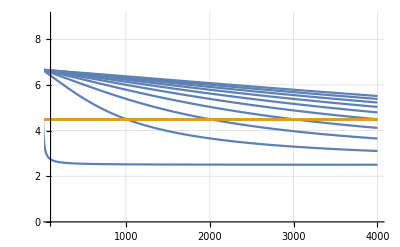

```mathematica
Show[Table[Plot[{MFPT[dl, kd, c, n, T] /. {T->8, n->5, c->2}, 4.5},{dl, 0,4000}, PlotRange->{{100, 4000}, {0, 9}}, GridLines->Automatic],{kd,10,10000,1000}]]
```

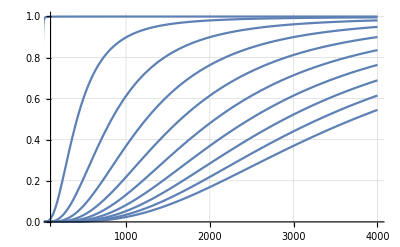

```mathematica
Show[Table[Plot[{factive[dl, kd, c, n, T] /. {T->8, n->5, c->2}, 4.5},{dl, 0,4000}, PlotRange->{{100, 4000}, {0, 1}}, GridLines->Automatic],{kd,10,10000,1000}]]
```

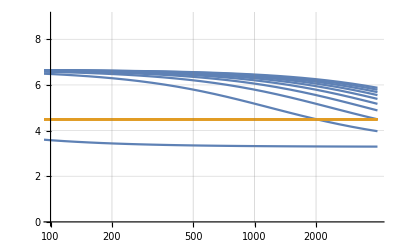

```mathematica
Show[Table[LogLinearPlot[{MFPT[dl, kd, c, n, T] /. {T->8, n->5, c->1.5}, 4.5},{dl, 0,4000}, PlotRange->{{100, 4000}, {0, 9}}, GridLines->Automatic],{kd,10,10000,1000}]]
```